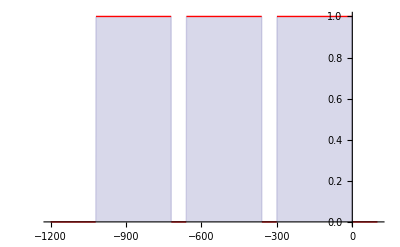

```mathematica
(* Decay heat calculation according to the simplified DIN25463-1990 formula *)
(* The decay heat calculation according to the 1990 formula is very simple as compared to
the updated standard from 2014. Old 1990 standard: "https://www.beuth.de/de/norm/din-25463-1/1549611"
New 2014 standard: "https://www.beuth.de/de/norm/din-25463-1/194886177" *)
(* The 1990 standard also contained a simplified formula which in essence is an evelope function
to cover different enrichments etc. *)
(* As input you have to define a power history as a step-wise function *)

gamma={
{7.552*10^-2,7.546*10^-2,7.602*10^-2},
{2.040*10^0,1.532*10^0,1.191*10^0},
{-1.991*10^-1,-1.934*10^-1,-1.918*10^-1}
};

a={
{9.023*10^-2,1.069*10^-1,1.207*10^-1},
{5.056*10^0,5.226*10^0,5.310*10^0},
{-1.659*10^+2,-1.705*10^+2,-1.624*10^+2},
{-5.716*10^+2,-8.356*10^+2,-9.077*10^+2},
{-1.022*10^+4,-1.127*10^+4,-1.126*10^+4},
{-6.498*10^+4,-7.328*10^+4,-7.644*10^+4}
};

b={
{2.611*10^+3,1.734*10^+3,1.389*10^+3},
{2.286*10^+6,2.158*10^+6,2.115*10^+6},
{2.389*10^+10,2.287*10^+10,2.214*10^+10},
{2.411*10^+13,1.764*10^+13,1.740*10^+13},
{6.881*10^+14,6.948*10^+14,6.904*10^+14},
{1.763*10^+16,1.846*10^+16,1.869*10^+16}
};

c={
{9.156*10^-5,1.717*10^-4,1.683*10^-4},
{-2.883*10^+1,-1.969*10^+1,-2.086*10^+1}
};

FAHC={
{0,1.027},
{1.0,1.028},{1.5,1.028},{2.0,1.029},{3.0,1.029},{4.0,1.030},{6.0,1.031},{8.0,1.031},
{10.0,1.033},{15.0,1.034},{20.0,1.034},{30.0,1.034},{40.0,1.035},
{60.0,1.037},{80.0,1.037},{100.0,1.037},{150.0,1.039},{200.0,1.041},{300.0,1.042},{400.0,1.044},{600.0,1.049},{800.0,1.052},{1000.0,1.055},{1500.0,1.059},{2000.0,1.063},{3000.0,1.070},{4000.0,1.075},{6000.0,1.084},{8000.0,1.091},{10000,1.097},{15000,1.109},{20000,1.118},{30000,1.131},{40000,1.142},{60000,1.158},{80000,1.168},{1.0*10^5,1.177},{1.5*10^5,1.188},{2.0*10^5,1.195},{3.0*10^5,1.201},{4.0*10^5,1.203},{6.0*10^5,1.206},{8.0*10^5,1.210},{1.0*10^6,1.213},{1.5*10^6,1.223},{2.0*10^6,1.231},{3.0*10^6,1.247},{4.0*10^6,1.258},{6.0*10^6,1.285},{8.0*10^6,1.310},{1.0*10^7,1.331},{1.5*10^7,1.378},{2.0*10^7,1.415},{3.0*10^7,1.466},{4.0*10^7,1.503},{6.0*10^7,1.565},{8.0*10^7,1.628},{1.0*10^8,1.691},{1.5*10^8,1.785},{2.0*10^8,1.799},{3.0*10^8,1.721}
};

BMAX={
{0,3.741*10^-3},{1.0,3.740*10^-3},{1.5,3.740*10^-3},{2.0,3.739*10^-3},
{3.0,3.738*10^-3},{4.0,3.737*10^-3},{6.0,3.736*10^-3},{8.0,3.734*10^-3},
{10.0,3.732*10^-3},{15.0,3.727*10^-3},{20.0,3.722*10^-3},{30.0,3.712*10^-3},
{40.0,3.703*10^-3},{60.0,3.684*10^-3},{80.0,3.665*10^-3},{100.0,3.646*10^-3},
{150.0,3.600*10^-3},{200.0,3.555*10^-3},{300.0,3.469*10^-3},{400.0,3.387*10^-3},
{600.0,3.233*10^-3},{800.0,3.095*10^-3},{1000.0,2.969*10^-3},{1500.0,2.702*10^-3},
{2000.0,2.493*10^-3},{3000.0,2.200*10^-3},{4000.0,2.019*10^-3},{6000.0,1.833*10^-3},
{8000.0,1.757*10^-3},{10000,1.721*10^-3},{15000,1.678*10^-3},{20000,1.649*10^-3},
{30000,1.594*10^-3},{40000,1.540*10^-3},{60000,1.439*10^-3},{80000,1.344*10^-3},
{1.0*10^5,1.255*10^-3},{1.5*10^5,1.058*10^-3},{2.0*10^5,8.925*10^-4},{3.0*10^5,6.346*10^-4},{4.0*10^5,4.512*10^-4},{6.0*10^5,2.281*10^-4},
{8.0*10^5,1.154*10^-4},{1.0*10^6,5.832*10^-5},{1.5*10^6,1.060*10^-5},
{2.0*10^6,1.927*10^-6},{3.0*10^6,6.367*10^-8},{4.0*10^6,2.104*10^-9},
{6.0*10^6,2.297*10^-12},{8.0*10^6,2.507*10^-15},{1.0*10^7,0.0},
{1.5*10^7,0.0},{2.0*10^7,0.0},{3.0*10^7,0.0},{4.0*10^7,0.0},{6.0*10^7,0.0},
{8.0*10^7,0.0},{1.0*10^8,0.0},{1.5*10^8,0.0},{2.0*10^8,0.0},{3.0*10^8,0.0}
};

FA=Interpolation[FAHC];
BM=Interpolation[BMAX];

(* n=1 is a conservative estimate of the upper bound of the decay heat assuming sigma=0 *)
(* n=2 is a conservative estimate of the upper bound of the decay heat assuming sigma=1 *)
(* n=3 is a conservative estimate of the upper bound of the decay heat assuming sigma=2 *)

Fv[t_,n_]:=gamma[[1]][[n]]*(gamma[[2]][[n]]+t)^(gamma[[3]][[n]])+c[[1]][[n]]*Exp[c[[2]][[n]]*t]+Sum[(a[[j]][[n]]/Sqrt[b[[j]][[n]]+t^2]),{j,1,6}];

(* the power history has to be defined in such a manner that t=0 equals end of life EOL *)

tk={300+60+300+60,300+60,0};
Tk={300,300,300};

power[t_]:=UnitStep[t+tk[[1]]+Tk[[1]]]-UnitStep[t+tk[[1]]]+UnitStep[t+tk[[2]]+Tk[[2]]]-UnitStep[t+tk[[2]]]+UnitStep[t+tk[[3]]+Tk[[3]]]-UnitStep[t+tk[[3]]];

Plot[power[t],{t,-1200,100},PlotStyle->{Red,Thick},Filling->Bottom]
```

```mathematica
DayToSec=24*60*60;

DecayHeat[t_,n_]:=FA[t]*Sum[(Fv[tk[[j]]*DayToSec+t,n]-Fv[(tk[[j]]+Tk[[j]])*DayToSec+t,n]),{j,1,3}]+BM[t];

results={
{0.1,DecayHeat[0.1,2] },
{1,DecayHeat[1,2] },
{10,DecayHeat[10,2] },
{100,DecayHeat[100,2] },
{1000,DecayHeat[1000,2] },
{10^4,DecayHeat[10^4,2] },
{10^5,DecayHeat[10^5,2] },
{10^6,DecayHeat[10^6,2] },
{10^7,DecayHeat[10^7,2] },
{10^8,DecayHeat[10^8,2] }
};

results
```

{{0.1,0.0764875},{1,0.0707629},{10,0.0544559},{100,0.0362458},{1000,0.0229125},{10000,0.0118817},{100000,0.00644069},{1000000,0.00274417},{10000000,0.000890494},{100000000,0.000110294}}

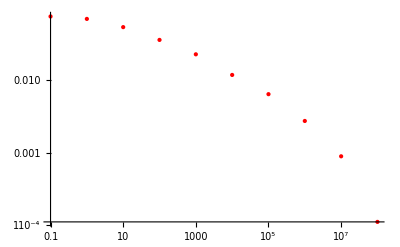

```mathematica
ListLogLogPlot[results,PlotStyle->{Red,Thick}]
```